```mathematica
∑_(i=1)^(m-1) (∑_(j=1)^i Subscript[a, j])^2
```

∑_(i=1)^(-1+m) (∑_(j=1)^i a_j)^2

```mathematica
FullSimplify[m^2∑_(i=1)^(m-1) Subscript[a, i]-m∑_(i=1)^(m-1) i Subscript[a, i]-m^2/2∑_(i=1)^(m-1) Subscript[a, i]+m/2∑_(i=1)^(m-1) Subscript[a, i]-1/2∑_(i=1)^(m-1) i Subscript[a, i]+1/2∑_(i=1)^(m-1) i^2 Subscript[a, i]-e m ∑_(i=1)^(m-1) Subscript[a, i]+e∑_(i=1)^(m-1) i Subscript[a, i]+∑_(i=1)^(m-1) (∑_(j=1)^i Subscript[a, j])^2]
```

1/2 (m (1-2 e+m) ∑_(i=1)^(-1+m) a_i+(-1+2 e-2 m) ∑_(i=1)^(-1+m) i a_i+∑_(i=1)^(-1+m) i^2 a_i+2 ∑_(i=1)^(-1+m) (∑_(j=1)^i a_j)^2)

```mathematica
m^2∑_(i=1)^(m-1) Subscript[a, i]-m∑_(i=1)^(m-1) i Subscript[a, i]-m^2/2∑_(i=1)^(m-1) Subscript[a, i]+m/2∑_(i=1)^(m-1) Subscript[a, i]-1/2∑_(i=1)^(m-1) i Subscript[a, i]+1/2∑_(i=1)^(m-1) i^2 Subscript[a, i]-e m ∑_(i=1)^(m-1) Subscript[a, i]+e∑_(i=1)^(m-1) i Subscript[a, i]+2(1/6 e (1+e) (1+2 e))

m^2∑_(i=1)^(m-1) Subscript[a, i]-m^2/2∑_(i=1)^(m-1) Subscript[a, i]+m/2∑_(i=1)^(m-1) Subscript[a, i]-e m ∑_(i=1)^(m-1) Subscript[a, i]

∑_(i=1)^(m-1) (1/2 i^2+(-m+e-1/2)i+(m^2-m^2/2+m/2-e m))Subscript[a, i]
```

```mathematica
Solve[D[(1/2 i^2+(-m+e-1/2)i+(m^2-m^2/2+m/2-e m)),i]==0,i]
```

{{i→1/2 (1-2 e+2 m)}}

```mathematica
fi[i_]:=(1/2 i^2+(-m+e-1/2)i+(m^2-m^2/2+m/2-e m))
```

```mathematica
Expand[1/2 (1-2 e+2 m)]
```

1/2-e+m

```mathematica
"The mins are 1-e-m and e-m and they're equal and going outward increases, just like before. Now just need to do cases and should get everything else, with a sweet lower bount on ∑_(i = 1)^(-1 + m) (∑_(j = 1)^i a_j)^2";
"Oh, also don't forget to prove that pretty awesome bound...";
```

```mathematica
Reduce[{fi[1-e+m]≠fi[-e+m],3≤e≤m},Integers]
```

False

```mathematica
Reduce[{fi[1-e+m+j]≤fi[1-e+m],j≥1,3≤e≤m},Integers]
```

False

```mathematica
Reduce[{fi[-e+m-k]≤fi[-e+m],k≥1,3≤e≤m},Integers]
```

False

```mathematica
Reduce[{fi[1-e+m+j]≠fi[-e+m-k],j≥1,k≥1,j==k,3≤e≤m},Integers]
```

False

```mathematica
Reduce[{3==e≤m,
(∑_(j=1)^1 fi[1-e+m+j])+fi[1-e+m]+fi[-e+m]+2(1/6 e (1+e) (1+2 e))≤a},a,Integers]
```

(a|m)∈Integers&&e==3&&m≥3&&a≥20

```mathematica
Reduce[{3==e≤m,
(∑_(k=1)^1 fi[-e+m-k])+fi[1-e+m]+fi[-e+m]+2(1/6 e (1+e) (1+2 e))≤a},a,Integers]
```

(a|m)∈Integers&&e==3&&m≥3&&a≥20

```mathematica
Simplify[Reduce[{4≤e≤m,
jm+km+2==e,
1≤1-e+m+jm≤m-1,
1≤-e+m-km≤m-1,
-1≤jm-km≤1,
(∑_(j=1)^jm fi[1-e+m+j])+(∑_(k=1)^km fi[-e+m-k])+fi[1-e+m]+fi[-e+m]+2(1/6 e (1+e) (1+2 e))≤a},a,Integers],(C[1]|C[2]|C[3])∈Integers&&m==C[2]&&a==C[3]]
```

(jm==1&&((e==4&&km==1&&C[2]≥6&&C[3]≥38)||(e==5&&km==2&&C[2]≥8&&C[3]≥65)))||(jm==C[1]&&C[1]≥2&&((e==1+2 C[1]&&1+km==C[1]&&3 C[1]<C[2]&&11+47 C[1]+51 C[1]^2+10 C[1]^3<6 C[3])||(e==2+2 C[1]&&km==C[1]&&2+3 C[1]<C[2]&&23+52 C[1]+33 C[1]^2+5 C[1]^3<3 C[3])||(e==3+2 C[1]&&km==1+C[1]&&4+3 C[1]<C[2]&&119+179 C[1]+81 C[1]^2+10 C[1]^3<6 C[3])))

```mathematica
LogicalExpand[%]
```

(e==4&&jm==1&&km==1&&C[2]≥6&&C[3]≥38)||(e==5&&jm==1&&km==2&&C[2]≥8&&C[3]≥65)||(C[1]==jm&&C[1]==km&&2+2 C[1]==e&&C[1]≥2&&2+3 C[1]<C[2]&&23+52 C[1]+33 C[1]^2+5 C[1]^3<3 C[3])||(C[1]==jm&&C[1]==1+km&&1+2 C[1]==e&&C[1]≥2&&3 C[1]<C[2]&&11+47 C[1]+51 C[1]^2+10 C[1]^3<6 C[3])||(C[1]==jm&&1+C[1]==km&&3+2 C[1]==e&&C[1]≥2&&4+3 C[1]<C[2]&&119+179 C[1]+81 C[1]^2+10 C[1]^3<6 C[3])

```mathematica
Reduce[{n≥3,3n+2>n^2},Integers]
```

n==3

```mathematica
∑_(i=1)^(m-1) (∑_(j=1)^i Subscript[a, j])^2
```

```mathematica
testtotextra[m_]:=Map[First,Block[{all=Table[Block[{a=PadLeft[IntegerDigits[x,2],m]},Block[{e=Total[a]},{m,e,∑_(i=1)^(m-1) (1/2 i^2+(-m+e-1/2)i+(m^2-m^2/2+m/2-e m))a[[i]]+∑_(i=1)^(m-1) (∑_(j=1)^i a[[j]])^2}]],{x,0,2^m-1}]},Table[MinimalBy[Select[all,#[[2]]==k&],Last],{k,0,m}]]]
```

```mathematica
testtotextra[2]
```

{{2,0,0},{2,1,0},{2,2,0}}

```mathematica
testtotextra[3]
```

{{3,0,0},{3,1,0},{3,2,0},{3,3,0}}

```mathematica
testtotextra[4]
```

{{4,0,0},{4,1,0},{4,2,0},{4,3,0},{4,4,0}}

```mathematica
testtotextra[5]
```

{{5,0,0},{5,1,0},{5,2,0},{5,3,0},{5,4,0},{5,5,0}}

```mathematica
testtotextra[6]
```

{{6,0,0},{6,1,0},{6,2,0},{6,3,0},{6,4,0},{6,5,0},{6,6,0}}

```mathematica
testtotextra[7]
```

{{7,0,0},{7,1,0},{7,2,0},{7,3,0},{7,4,0},{7,5,0},{7,6,0},{7,7,0}}

```mathematica
testtotextra[8]
```

{{8,0,0},{8,1,0},{8,2,0},{8,3,0},{8,4,0},{8,5,0},{8,6,0},{8,7,0},{8,8,0}}

```mathematica
testtotextra[9]
```

{{9,0,0},{9,1,0},{9,2,0},{9,3,0},{9,4,0},{9,5,0},{9,6,0},{9,7,0},{9,8,0},{9,9,0}}

```mathematica
domin[f_,from_,to_]:=Block[{min=∞,thisval=0},
Do[thisval=f[j];If[thisval<min,min=thisval,0],{j,from,to}];min]
```

```mathematica
testtot[m_]:=Map[First,Block[{all=Table[Block[{a=PadLeft[IntegerDigits[x,2],m]},Block[{e=Total[a]},{m,e,∑_(i=1)^(m-1) (1/2 i^2+(-m+e-1/2)i+(m^2-m^2/2+m/2-e m))a[[i]]}]],{x,0,2^m-1}]},Table[MinimalBy[Select[all,#[[2]]==k&],Last],{k,0,m}]]]
```

```mathematica
Timing[Monitor[testtot[2],j]]
```

{0.001318,{{2,0,0},{2,1,0},{2,2,-1}}}

```mathematica
Timing[Monitor[testtot[3],j]]
```

{0.001535,{{3,0,0},{3,1,0},{3,2,-2},{3,3,-5}}}

```mathematica
Timing[Monitor[testtot[4],j]]
```

{0.002758,{{4,0,0},{4,1,0},{4,2,-2},{4,3,-8},{4,4,-14}}}

```mathematica
Timing[Monitor[testtot[5],j]]
```

{0.003336,{{5,0,0},{5,1,0},{5,2,-2},{5,3,-8},{5,4,-20},{5,5,-30}}}

```mathematica
Timing[Monitor[testtot[6],j]]
```

{0.005061,{{6,0,0},{6,1,0},{6,2,-2},{6,3,-8},{6,4,-22},{6,5,-40},{6,6,-55}}}

```mathematica
Timing[Monitor[testtot[7],j]]
```

{0.010093,{{7,0,0},{7,1,0},{7,2,-2},{7,3,-8},{7,4,-22},{7,5,-45},{7,6,-70},{7,7,-91}}}

```mathematica
Timing[Monitor[testtot[8],j]]
```

{0.020159,{{8,0,0},{8,1,0},{8,2,-2},{8,3,-8},{8,4,-22},{8,5,-45},{8,6,-79},{8,7,-112},{8,8,-140}}}

```mathematica
Timing[Monitor[testtot[9],j]]
```

{0.044105,{{9,0,0},{9,1,0},{9,2,-2},{9,3,-8},{9,4,-22},{9,5,-45},{9,6,-82},{9,7,-126},{9,8,-168},{9,9,-204}}}

```mathematica
Timing[Monitor[testtot[10],j]]
```

{0.099958,{{10,0,0},{10,1,0},{10,2,-2},{10,3,-8},{10,4,-22},{10,5,-45},{10,6,-82},{10,7,-133},{10,8,-188},{10,9,-240},{10,10,-285}}}

```mathematica
Timing[Monitor[testtot[11],j]]
```

{0.231114,{{11,0,0},{11,1,0},{11,2,-2},{11,3,-8},{11,4,-22},{11,5,-45},{11,6,-82},{11,7,-133},{11,8,-200},{11,9,-267},{11,10,-330},{11,11,-385}}}

```mathematica
Timing[Monitor[testtot[12],j]]
```

{0.473864,{{12,0,0},{12,1,0},{12,2,-2},{12,3,-8},{12,4,-22},{12,5,-45},{12,6,-82},{12,7,-133},{12,8,-204},{12,9,-285},{12,10,-365},{12,11,-440},{12,12,-506}}}

```mathematica
Timing[Monitor[testtot[13],j]]
```

{1.032,{{13,0,0},{13,1,0},{13,2,-2},{13,3,-8},{13,4,-22},{13,5,-45},{13,6,-82},{13,7,-133},{13,8,-204},{13,9,-294},{13,10,-390},{13,11,-484},{13,12,-572},{13,13,-650}}}

```mathematica
Timing[Monitor[testtot[14],j]]
```

{2.09737,{{14,0,0},{14,1,0},{14,2,-2},{14,3,-8},{14,4,-22},{14,5,-45},{14,6,-82},{14,7,-133},{14,8,-204},{14,9,-294},{14,10,-405},{14,11,-517},{14,12,-626},{14,13,-728},{14,14,-819}}}

```mathematica
Timing[Monitor[testtot[15],j]]
```

{4.75864,{{15,0,0},{15,1,0},{15,2,-2},{15,3,-8},{15,4,-22},{15,5,-45},{15,6,-82},{15,7,-133},{15,8,-204},{15,9,-294},{15,10,-410},{15,11,-539},{15,12,-668},{15,13,-793},{15,14,-910},{15,15,-1015}}}

```mathematica
Timing[Monitor[testtot[16],j]]
```

{9.48345,{{16,0,0},{16,1,0},{16,2,-2},{16,3,-8},{16,4,-22},{16,5,-45},{16,6,-82},{16,7,-133},{16,8,-204},{16,9,-294},{16,10,-410},{16,11,-550},{16,12,-698},{16,13,-845},{16,14,-987},{16,15,-1120},{16,16,-1240}}}

```mathematica
Timing[Monitor[testtot[17],j]]
```

{21.0085,{{17,0,0},{17,1,0},{17,2,-2},{17,3,-8},{17,4,-22},{17,5,-45},{17,6,-82},{17,7,-133},{17,8,-204},{17,9,-294},{17,10,-410},{17,11,-550},{17,12,-716},{17,13,-884},{17,14,-1050},{17,15,-1210},{17,16,-1360},{17,17,-1496}}}

```mathematica
Timing[Monitor[testtot[18],j]]
```

{44.9632,{{18,0,0},{18,1,0},{18,2,-2},{18,3,-8},{18,4,-22},{18,5,-45},{18,6,-82},{18,7,-133},{18,8,-204},{18,9,-294},{18,10,-410},{18,11,-550},{18,12,-722},{18,13,-910},{18,14,-1099},{18,15,-1285},{18,16,-1464},{18,17,-1632},{18,18,-1785}}}

```mathematica
Timing[Monitor[testtot[19],j]]
```

{99.9155,{{19,0,0},{19,1,0},{19,2,-2},{19,3,-8},{19,4,-22},{19,5,-45},{19,6,-82},{19,7,-133},{19,8,-204},{19,9,-294},{19,10,-410},{19,11,-550},{19,12,-722},{19,13,-923},{19,14,-1134},{19,15,-1345},{19,16,-1552},{19,17,-1751},{19,18,-1938},{19,19,-2109}}}

```mathematica
Timing[Monitor[testtot[20],j]]
```

{202.326,{{20,0,0},{20,1,0},{20,2,-2},{20,3,-8},{20,4,-22},{20,5,-45},{20,6,-82},{20,7,-133},{20,8,-204},{20,9,-294},{20,10,-410},{20,11,-550},{20,12,-722},{20,13,-923},{20,14,-1155},{20,15,-1390},{20,16,-1624},{20,17,-1853},{20,18,-2073},{20,19,-2280},{20,20,-2470}}}

```mathematica
Timing[Monitor[testtot[21],j]]
```

{440.472,{{21,0,0},{21,1,0},{21,2,-2},{21,3,-8},{21,4,-22},{21,5,-45},{21,6,-82},{21,7,-133},{21,8,-204},{21,9,-294},{21,10,-410},{21,11,-550},{21,12,-722},{21,13,-923},{21,14,-1162},{21,15,-1420},{21,16,-1680},{21,17,-1938},{21,18,-2190},{21,19,-2432},{21,20,-2660},{21,21,-2870}}}

```mathematica
Timing[Monitor[testtot[22],j]]
```

```mathematica
Timing[Monitor[testtot[23],j]]
```

```mathematica
Timing[Monitor[testtot[24],j]]
```

```mathematica
Timing[Monitor[testtot[25],j]]
```

```mathematica
Timing[Monitor[testtot[26],j]]
```

```mathematica
Timing[Monitor[testtot[27],j]]
```

```mathematica
Map[Last,Table[Last[Out[i]],{i,246,265}],{2}]//Column
```

{0,0,-1}
{0,0,-2,-5}
{0,0,-2,-8,-14}
{0,0,-2,-8,-20,-30}
{0,0,-2,-8,-22,-40,-55}
{0,0,-2,-8,-22,-45,-70,-91}
{0,0,-2,-8,-22,-45,-79,-112,-140}
{0,0,-2,-8,-22,-45,-82,-126,-168,-204}
{0,0,-2,-8,-22,-45,-82,-133,-188,-240,-285}
{0,0,-2,-8,-22,-45,-82,-133,-200,-267,-330,-385}
{0,0,-2,-8,-22,-45,-82,-133,-204,-285,-365,-440,-506}
{0,0,-2,-8,-22,-45,-82,-133,-204,-294,-390,-484,-572,-650}
{0,0,-2,-8,-22,-45,-82,-133,-204,-294,-405,-517,-626,-728,-819}
{0,0,-2,-8,-22,-45,-82,-133,-204,-294,-410,-539,-668,-793,-910,-1015}
{0,0,-2,-8,-22,-45,-82,-133,-204,-294,-410,-550,-698,-845,-987,-1120,-1240}
{0,0,-2,-8,-22,-45,-82,-133,-204,-294,-410,-550,-716,-884,-1050,-1210,-1360,-1496}
{0,0,-2,-8,-22,-45,-82,-133,-204,-294,-410,-550,-722,-910,-1099,-1285,-1464,-1632,-1785}
{0,0,-2,-8,-22,-45,-82,-133,-204,-294,-410,-550,-722,-923,-1134,-1345,-1552,-1751,-1938,-2109}
{0,0,-2,-8,-22,-45,-82,-133,-204,-294,-410,-550,-722,-923,-1155,-1390,-1624,-1853,-2073,-2280,-2470}
{0,0,-2,-8,-22,-45,-82,-133,-204,-294,-410,-550,-722,-923,-1162,-1420,-1680,-1938,-2190,-2432,-2660,-2870}

```mathematica
Expand[InterpolatingPolynomial[{2,8,22,45,82,133,204,294,410,550,722,923},x]]
```

1792-(72858353 x)/13860+(11417383 x^2)/1800-(95983189 x^3)/22680+(997427 x^4)/567-(912337 x^5)/1890+(242731 x^6)/2700-(8641 x^7)/756+(211 x^8)/216-(1217 x^9)/22680+(97 x^10)/56700-x^11/41580

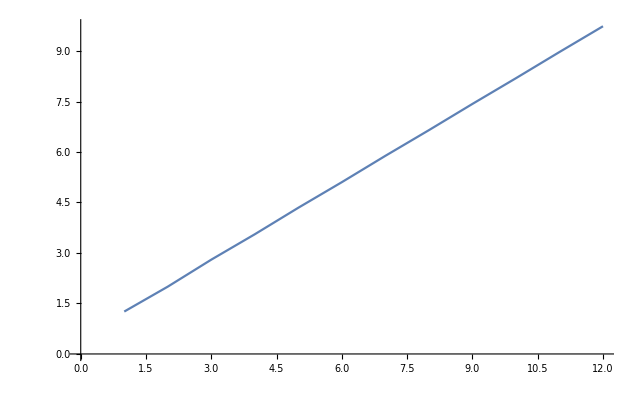

```mathematica
ListPlot[Map[#^(1/3)&,{2,8,22,45,82,133,204,294,410,550,722,923}],Joined->True]
```

```mathematica
Fit[{2,8,22,45,82,133,204,294,410,550,722,923}, {1,x,x^2,x^3}, x]
```

0.424242+0.186092 x+0.934732 x^2+0.454934 x^3

```mathematica
NonlinearModelFit[{2,8,22,45,82,133,204,294,410,550,722,923},a+b x+c x^2+d x^3,{a,b,c,d},x]
```

```mathematica
FittedModel[0.42424242424256964+0.18609168609164195 x+0.9347319347319482 x^2+0.4549339549339542 x^3]["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
a | 0.424242 | 0.991327 | {-1.86176,2.71025}
b | 0.186092 | 0.633907 | {-1.2757,1.64788}
c | 0.934732 | 0.111029 | {0.678699,1.19077}
d | 0.454934 | 0.00562991 | {0.441951,0.467917}

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableMeanSquares,ANOVATableSumsOfSquares,BestFit,BestFitParameters,BIC,CorrelationMatrix,CovarianceMatrix,CurvatureConfidenceRegion,Data,EstimatedVariance,FitCurvatureTable,FitCurvatureTableEntries,FitResiduals,Function,HatDiagonal,MaxIntrinsicCurvature,MaxParameterEffectsCurvature,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterBias,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PredictedResponse,Properties,Response,RSquared,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals}

```mathematica
First[Out[267]]
InterpolatingPolynomial[Map[{{#[[1]],#[[2]]},#[[3]]}&,%],{m,e}]
```

{{2,0,0},{2,1,0},{2,2,-1}}

InterpolatingPolynomial::poised: The interpolation points {{2, 0}, {2, 1}, {2, 2}} are not poised, so an interpolating polynomial of total degree 1 could not be found.

InterpolatingPolynomial[{{{2,0},0},{{2,1},0},{{2,2},-1}},{m,e}]

```mathematica
InterpolatingPolynomial[%,m]
```

1+(4+(5/2+1/3 (-3+m)) (-2+m)) (-1+m)

```mathematica
Expand[Simplify[Expand[ ∑_(i=1)^3 (∑_(j=1)^i Subscript[a, j])^2],Subscript[a, 1]^2==Subscript[a, 1]&&Subscript[a, 2]^2==Subscript[a, 2]&&Subscript[a, 3]^2==Subscript[a, 3]]]
```

3 a_1+2 a_2+4 a_1 a_2+a_3+2 a_1 a_3+2 a_2 a_3

```mathematica
First[Table[ Expand[Simplify[Expand[ ∑_(i=1)^m (∑_(j=1)^i Subscript[a, j])^2],Fold[#1&&#2&,True,Table[Subscript[a, i]^2==Subscript[a, i],{i,1,m}]]]],{m,20,20}]]
```

20 a_1+19 a_2+38 a_1 a_2+18 a_3+36 a_1 a_3+36 a_2 a_3+17 a_4+34 a_1 a_4+34 a_2 a_4+34 a_3 a_4+16 a_5+32 a_1 a_5+32 a_2 a_5+32 a_3 a_5+32 a_4 a_5+15 a_6+30 a_1 a_6+30 a_2 a_6+30 a_3 a_6+30 a_4 a_6+30 a_5 a_6+14 a_7+28 a_1 a_7+28 a_2 a_7+28 a_3 a_7+28 a_4 a_7+28 a_5 a_7+28 a_6 a_7+13 a_8+26 a_1 a_8+26 a_2 a_8+26 a_3 a_8+26 a_4 a_8+26 a_5 a_8+26 a_6 a_8+26 a_7 a_8+12 a_9+24 a_1 a_9+24 a_2 a_9+24 a_3 a_9+24 a_4 a_9+24 a_5 a_9+24 a_6 a_9+24 a_7 a_9+24 a_8 a_9+11 a_10+22 a_1 a_10+22 a_2 a_10+22 a_3 a_10+22 a_4 a_10+22 a_5 a_10+22 a_6 a_10+22 a_7 a_10+22 a_8 a_10+22 a_9 a_10+10 a_11+20 a_1 a_11+20 a_2 a_11+20 a_3 a_11+20 a_4 a_11+20 a_5 a_11+20 a_6 a_11+20 a_7 a_11+20 a_8 a_11+20 a_9 a_11+20 a_10 a_11+9 a_12+18 a_1 a_12+18 a_2 a_12+18 a_3 a_12+18 a_4 a_12+18 a_5 a_12+18 a_6 a_12+18 a_7 a_12+18 a_8 a_12+18 a_9 a_12+18 a_10 a_12+18 a_11 a_12+8 a_13+16 a_1 a_13+16 a_2 a_13+16 a_3 a_13+16 a_4 a_13+16 a_5 a_13+16 a_6 a_13+16 a_7 a_13+16 a_8 a_13+16 a_9 a_13+16 a_10 a_13+16 a_11 a_13+16 a_12 a_13+7 a_14+14 a_1 a_14+14 a_2 a_14+14 a_3 a_14+14 a_4 a_14+14 a_5 a_14+14 a_6 a_14+14 a_7 a_14+14 a_8 a_14+14 a_9 a_14+14 a_10 a_14+14 a_11 a_14+14 a_12 a_14+14 a_13 a_14+6 a_15+12 a_1 a_15+12 a_2 a_15+12 a_3 a_15+12 a_4 a_15+12 a_5 a_15+12 a_6 a_15+12 a_7 a_15+12 a_8 a_15+12 a_9 a_15+12 a_10 a_15+12 a_11 a_15+12 a_12 a_15+12 a_13 a_15+12 a_14 a_15+5 a_16+10 a_1 a_16+10 a_2 a_16+10 a_3 a_16+10 a_4 a_16+10 a_5 a_16+10 a_6 a_16+10 a_7 a_16+10 a_8 a_16+10 a_9 a_16+10 a_10 a_16+10 a_11 a_16+10 a_12 a_16+10 a_13 a_16+10 a_14 a_16+10 a_15 a_16+4 a_17+8 a_1 a_17+8 a_2 a_17+8 a_3 a_17+8 a_4 a_17+8 a_5 a_17+8 a_6 a_17+8 a_7 a_17+8 a_8 a_17+8 a_9 a_17+8 a_10 a_17+8 a_11 a_17+8 a_12 a_17+8 a_13 a_17+8 a_14 a_17+8 a_15 a_17+8 a_16 a_17+3 a_18+6 a_1 a_18+6 a_2 a_18+6 a_3 a_18+6 a_4 a_18+6 a_5 a_18+6 a_6 a_18+6 a_7 a_18+6 a_8 a_18+6 a_9 a_18+6 a_10 a_18+6 a_11 a_18+6 a_12 a_18+6 a_13 a_18+6 a_14 a_18+6 a_15 a_18+6 a_16 a_18+6 a_17 a_18+2 a_19+4 a_1 a_19+4 a_2 a_19+4 a_3 a_19+4 a_4 a_19+4 a_5 a_19+4 a_6 a_19+4 a_7 a_19+4 a_8 a_19+4 a_9 a_19+4 a_10 a_19+4 a_11 a_19+4 a_12 a_19+4 a_13 a_19+4 a_14 a_19+4 a_15 a_19+4 a_16 a_19+4 a_17 a_19+4 a_18 a_19+a_20+2 a_1 a_20+2 a_2 a_20+2 a_3 a_20+2 a_4 a_20+2 a_5 a_20+2 a_6 a_20+2 a_7 a_20+2 a_8 a_20+2 a_9 a_20+2 a_10 a_20+2 a_11 a_20+2 a_12 a_20+2 a_13 a_20+2 a_14 a_20+2 a_15 a_20+2 a_16 a_20+2 a_17 a_20+2 a_18 a_20+2 a_19 a_20

```mathematica
CoefficientArrays[%]
```

{0,SparseArray[<20>, {20}],SparseArray[<190>, {20, 20}]}

```mathematica
Map[Normal,%]
```

{0,{20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{{0,38,36,34,32,30,28,26,24,22,20,18,16,14,12,10,8,6,4,2},{0,0,36,34,32,30,28,26,24,22,20,18,16,14,12,10,8,6,4,2},{0,0,0,34,32,30,28,26,24,22,20,18,16,14,12,10,8,6,4,2},{0,0,0,0,32,30,28,26,24,22,20,18,16,14,12,10,8,6,4,2},{0,0,0,0,0,30,28,26,24,22,20,18,16,14,12,10,8,6,4,2},{0,0,0,0,0,0,28,26,24,22,20,18,16,14,12,10,8,6,4,2},{0,0,0,0,0,0,0,26,24,22,20,18,16,14,12,10,8,6,4,2},{0,0,0,0,0,0,0,0,24,22,20,18,16,14,12,10,8,6,4,2},{0,0,0,0,0,0,0,0,0,22,20,18,16,14,12,10,8,6,4,2},{0,0,0,0,0,0,0,0,0,0,20,18,16,14,12,10,8,6,4,2},{0,0,0,0,0,0,0,0,0,0,0,18,16,14,12,10,8,6,4,2},{0,0,0,0,0,0,0,0,0,0,0,0,16,14,12,10,8,6,4,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,14,12,10,8,6,4,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,10,8,6,4,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,8,6,4,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8,6,4,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,4,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
MatrixForm[Last[%]]
```

(0 | 38 | 36 | 34 | 32 | 30 | 28 | 26 | 24 | 22 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 36 | 34 | 32 | 30 | 28 | 26 | 24 | 22 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 34 | 32 | 30 | 28 | 26 | 24 | 22 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 32 | 30 | 28 | 26 | 24 | 22 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 30 | 28 | 26 | 24 | 22 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 28 | 26 | 24 | 22 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 26 | 24 | 22 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24 | 22 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Table[ Expand[Simplify[Expand[ ∑_(i=1)^m (∑_(j=1)^i Subscript[a, j])^2],Fold[#1&&#2&,True,Table[Subscript[a, i]^2==Subscript[a, i],{i,1,m}]]]],{m,2,4}]
```

{2 a_1+a_2+2 a_1 a_2,3 a_1+2 a_2+4 a_1 a_2+a_3+2 a_1 a_3+2 a_2 a_3,4 a_1+3 a_2+6 a_1 a_2+2 a_3+4 a_1 a_3+4 a_2 a_3+a_4+2 a_1 a_4+2 a_2 a_4+2 a_3 a_4}

```mathematica
Flatten[Table[{Subscript[a, 1]+Subscript[a, 2]+Subscript[a, 3],3 Subscript[a, 1]+2 Subscript[a, 2]+4 Subscript[a, 1] Subscript[a, 2]+Subscript[a, 3]+2 Subscript[a, 1] Subscript[a, 3]+2 Subscript[a, 2] Subscript[a, 3]},{Subscript[a, 1],0,1},{Subscript[a, 2],0,1},{Subscript[a, 3],0,1}],3-1]
```

{{0,0},{1,1},{1,2},{2,5},{1,3},{2,6},{2,9},{3,14}}

```mathematica
bestofM[m_]:=Block[{poly={Sum[Subscript[a, i],{i,1,m}],Expand[Simplify[Expand[ ∑_(i=1)^m (∑_(j=1)^i Subscript[a, j])^2],Fold[#1&&#2&,True,Table[Subscript[a, i]^2==Subscript[a, i],{i,1,m}]]]]}},
Map[First,Map[MinimalBy[#,Last]&,Table[Select[Table[Block[{vec=PadLeft[IntegerDigits[x,2],m]},
ReplaceAll[poly,Table[Subscript[a, i]->vec[[i]],{i,1,m}]]],{x,0,2^m-1}],First[#]==j&],{j,0,m}]]]]
```

```mathematica
Monitor[Timing[bestofM[2]],x]
```

{0.001245,{{0,0},{1,1},{2,5}}}

```mathematica
Monitor[Timing[bestofM[3]],x]
```

{0.002988,{{0,0},{1,1},{2,5},{3,14}}}

```mathematica
Monitor[Timing[bestofM[4]],x]
```

{0.054377,{{0,0},{1,1},{2,5},{3,14},{4,30}}}

```mathematica
Monitor[Timing[bestofM[5]],x]
```

{0.086327,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55}}}

```mathematica
Monitor[Timing[bestofM[6]],x]
```

{0.130431,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91}}}

```mathematica
Monitor[Timing[bestofM[7]],x]
```

{0.249962,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140}}}

```mathematica
Monitor[Timing[bestofM[8]],x]
```

{0.460461,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204}}}

```mathematica
Monitor[Timing[bestofM[9]],x]
```

{1.02633,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285}}}

```mathematica
Monitor[Timing[bestofM[10]],x]
```

{2.36009,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385}}}

```mathematica
Monitor[Timing[bestofM[11]],x]
```

{6.26003,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385},{11,506}}}

```mathematica
Monitor[Timing[bestofM[12]],x]
```

{15.8186,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385},{11,506},{12,650}}}

```mathematica
Monitor[Timing[bestofM[13]],x]
```

{39.8146,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385},{11,506},{12,650},{13,819}}}

```mathematica
Monitor[Timing[bestofM[14]],x]
```

{100.071,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385},{11,506},{12,650},{13,819},{14,1015}}}

```mathematica
Monitor[Timing[bestofM[15]],x]
```

{250.973,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385},{11,506},{12,650},{13,819},{14,1015},{15,1240}}}

```mathematica
Monitor[Timing[bestofM[16]],x]
```

$Aborted

```mathematica
Monitor[Timing[bestofM[17]],x]
```

```mathematica
Monitor[Timing[bestofM[18]],x]
```

```mathematica
Monitor[Timing[bestofM[19]],x]
```

```mathematica
Monitor[Timing[bestofM[20]],x]
```

```mathematica
Monitor[Timing[bestofM[21]],x]
```

```mathematica
Monitor[Timing[bestofM[22]],x]
```

```mathematica
Monitor[Timing[bestofM[23]],x]
```

```mathematica
Map[Last,{{0.001245,{{0,0},{1,1},{2,5}}},
{0.002988,{{0,0},{1,1},{2,5},{3,14}}},
{0.054377,{{0,0},{1,1},{2,5},{3,14},{4,30}}},
{0.086327,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55}}},
{0.130431,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91}}},
{0.249962,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140}}},
{0.460461,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204}}},
{1.026327,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285}}},
{2.360092,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385}}},
{6.260026,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385},{11,506}}},
{15.81857,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385},{11,506},{12,650}}},
{39.814592,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385},{11,506},{12,650},{13,819}}},
{100.071034,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385},{11,506},{12,650},{13,819},{14,1015}}},
{250.972517,{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385},{11,506},{12,650},{13,819},{14,1015},{15,1240}}}}]//Last
```

{{0,0},{1,1},{2,5},{3,14},{4,30},{5,55},{6,91},{7,140},{8,204},{9,285},{10,385},{11,506},{12,650},{13,819},{14,1015},{15,1240}}

```mathematica
InterpolatingPolynomial[%,e]
```

(1+(3/2+1/3 (-2+e)) (-1+e)) e

```mathematica
FullSimplify[%]
```

1/6 e (1+e) (1+2 e)

```mathematica
∑_(i=1)^(m-1) (∑_(j=1)^i Subscript[a, j])^2≥1/6 e (1+e) (1+2 e)
```

```mathematica
bestofM[m_]:=Block[{poly={Sum[Subscript[a, i],{i,1,m}],Expand[Simplify[Expand[ ∑_(i=1)^m (∑_(j=1)^i Subscript[a, j])^2],Fold[#1&&#2&,True,Table[Subscript[a, i]^2==Subscript[a, i],{i,1,m}]]]]}},
Map[First,Map[MinimalBy[#,Last]&,Table[Select[Table[Block[{vec=PadLeft[IntegerDigits[x,2],m]},
ReplaceAll[poly,Table[Subscript[a, i]->vec[[i]],{i,1,m}]]],{x,0,2^m-1}],First[#]==j&],{j,0,m}]]]]
```

```mathematica
bestofM2[m_]:=Map[MinimalBy[#,Last]&,Table[Select[Block[{poly={x,Sum[Subscript[a, i],{i,1,m}],Expand[Simplify[Expand[ ∑_(i=1)^m (∑_(j=1)^i Subscript[a, j])^2],Fold[#1&&#2&,True,Table[Subscript[a, i]^2==Subscript[a, i],{i,1,m}]]]]}},
Table[Block[{vec=PadLeft[IntegerDigits[x,2],m]},
ReplaceAll[poly,Table[Subscript[a, i]->vec[[i]],{i,1,m}]]],{x,0,2^m-1}]],#[[2]]==j&],{j,0,m}]]
```

```mathematica
bestofM2[3]
```

{{{0,0,0}},{{1,1,1}},{{3,2,5}},{{7,3,14}}}

```mathematica
bestofM2[4]
```

{{{0,0,0}},{{1,1,1}},{{3,2,5}},{{7,3,14}},{{15,4,30}}}

```mathematica
bestofM2[5]
```

{{{0,0,0}},{{1,1,1}},{{3,2,5}},{{7,3,14}},{{15,4,30}},{{31,5,55}}}

```mathematica
bestofM2[6]
```

{{{0,0,0}},{{1,1,1}},{{3,2,5}},{{7,3,14}},{{15,4,30}},{{31,5,55}},{{63,6,91}}}

```mathematica
bestofM3[m_]:=Map[First,Map[MinimalBy[#,Last]&,Table[Select[Block[{poly={x,Sum[Subscript[a, i],{i,1,m}],Expand[Simplify[Expand[ ∑_(i=1)^m (∑_(j=1)^i Subscript[a, j])^2],Fold[#1&&#2&,True,Table[Subscript[a, i]^2==Subscript[a, i],{i,1,m}]]]]}},
Table[Block[{vec=PadLeft[IntegerDigits[x,2],m]},
ReplaceAll[poly,Table[Subscript[a, i]->vec[[i]],{i,1,m}]]],{x,0,2^m-1}]],#[[2]]==j&],{j,0,m}]]]
```

```mathematica
bestofM3[2]
```

{{0,0,0},{1,1,1},{3,2,5}}

```mathematica
bestofM3[3]
```

{{0,0,0},{1,1,1},{3,2,5},{7,3,14}}

```mathematica
bestofM3[4]
```

{{0,0,0},{1,1,1},{3,2,5},{7,3,14},{15,4,30}}

```mathematica
bestofM3[5]
```

{{0,0,0},{1,1,1},{3,2,5},{7,3,14},{15,4,30},{31,5,55}}

```mathematica
bestofM3[6]
```

{{0,0,0},{1,1,1},{3,2,5},{7,3,14},{15,4,30},{31,5,55},{63,6,91}}

```mathematica
Monitor[bestofM3[16],{x,j}]
```

{{0,0,0},{1,1,1},{3,2,5},{7,3,14},{15,4,30},{31,5,55},{63,6,91},{127,7,140},{255,8,204},{511,9,285},{1023,10,385},{2047,11,506},{4095,12,650},{8191,13,819},{16383,14,1015},{32767,15,1240},{65535,16,1496}}

```mathematica
Map[FactorInteger[First[#]+1]&,Out[103]]
```

{{{1,1}},{{2,1}},{{2,2}},{{2,3}},{{2,4}},{{2,5}},{{2,6}},{{2,7}},{{2,8}},{{2,9}},{{2,10}},{{2,11}},{{2,12}},{{2,13}},{{2,14}},{{2,15}},{{2,16}}}

```mathematica
"minimum is when the top ϵ are 1 and rest are 0."
```

```mathematica
∑_(i=1)^m (∑_(j=1)^i Subscript[a, j])^2

e==1
 ∑_(i=m)^m (∑_(j=m)^m 1)^2

e==2
 ∑_(i=m-1)^m (∑_(j=m-1)^i 1)^2

e==3
 ∑_(i=m-2)^m (∑_(j=m-2)^i 1)^2

e
 ∑_(i=m-(e-1))^m (∑_(j=m-(e-1))^i 1)^2
```

```mathematica
∑_(i=m-(e-1))^m (∑_(j=m-(e-1))^i 1)^2
```

1/6 e (1+e) (1+2 e)

```mathematica
"
Want:
	There is only one minimal solution for e
	All minimal solutions for (e+1) are minimal solutions for e plus one added '1'
	A minimal solution for m is a minimal solution for (m+1)

∑_(i = 1)^m (∑_(j = 1)^i a_(m + 1 - j))^2==(∑_(i = 1)^m k a_i)+∑_(i = 1)^m (∑_(j = 1)^(i - 1) 2j a_ja_i)
	
	Increasing m only extends right, doesn't affect so far.
	All minimal solutions for (e+1) are minimal solutions for e plus one added '1'
		e==1 → a_1==1
		suppose lowest e are filled. then adding one to any but lowest empty adds more than non-lowest.
		→ Min when lowest (e+1) filled.
"
```

```mathematica
∑_(i=1)^m (∑_(j=1)^i Subscript[a, j])^2
```

```mathematica
k==1->j==m+1-k==m
k==m+1-j
```

```mathematica
Table[∑_(i=1)^m (∑_(j=1)^i Subscript[a, j])^2,{m,2,2}]
```

{a_1^2+(a_1+a_2)^2}

```mathematica
First[Table[Expand[Simplify[Expand[ ∑_(i=1)^m (∑_(j=1)^i Subscript[a, m+1-j])^2],Fold[#1&&#2&,True,Table[Subscript[a, i]^2==Subscript[a, i],{i,1,m}]]]],{m,5,5}]]
```

a_1+2 a_2+2 a_1 a_2+3 a_3+2 a_1 a_3+4 a_2 a_3+4 a_4+2 a_1 a_4+4 a_2 a_4+6 a_3 a_4+5 a_5+2 a_1 a_5+4 a_2 a_5+6 a_3 a_5+8 a_4 a_5

```mathematica
First[Table[ReplaceAll[Expand[Simplify[Expand[ ∑_(i=1)^m (∑_(j=1)^i Subscript[a, j])^2],Fold[#1&&#2&,True,Table[Subscript[a, i]^2==Subscript[a, i],{i,1,m}]]]],Table[Subscript[a, i]->Subscript[a, m+1-i],{i,1,m}]],{m,5,5}]]
```

a_1+2 a_2+2 a_1 a_2+3 a_3+2 a_1 a_3+4 a_2 a_3+4 a_4+2 a_1 a_4+4 a_2 a_4+6 a_3 a_4+5 a_5+2 a_1 a_5+4 a_2 a_5+6 a_3 a_5+8 a_4 a_5

```mathematica
1,2->2
```

```mathematica
1,2->2
1,3->2
2,3->4
```

```mathematica
InterpolatingPolynomial[{{{1,2},2},{{1,3},2},{{2,3},4},{{1,4},2},{{2,4},4},{{3,4},6},{{1,5},2},{{2,5},4},{{3,5},6},{{4,5},8}},{i,j}]
```

2 i

```mathematica
Reduce[{∑_(i=1)^m (∑_(j=1)^i Subscript[a, m+1-j])^2==(∑_(i=1)^m k Subscript[a, i])+∑_(i=1)^m (∑_(j=1)^(i-1) 2j Subscript[a, j] Subscript[a, i]),m≥2}]
```

```mathematica
(∑_(i=1)^m k Subscript[a, i])+∑_(i=1)^m (∑_(j=1)^(i-1) 2j Subscript[a, j] Subscript[a, i])
```

```mathematica
Table[∑_(i=2)^m (∑_(j=1)^(i-1) 2j Subscript[a, i] Subscript[a, j]),{m,4,4}]
```

{2 a_1 a_2+2 a_1 a_3+4 a_2 a_3+2 a_1 a_4+4 a_2 a_4+6 a_3 a_4}

```mathematica
ReplaceAll[%,{Subscript[a, 1]->Subscript[a, 2],Subscript[a, 2]->Subscript[a, 1]}]
```

a_1+2 a_2+2 a_1 a_2

```mathematica
InterpolatingPolynomial[Reverse[Range[1,10]],k]
```

11-k

```mathematica
∑_(i=a)^b 1
```

1-a+b

```mathematica
FullSimplify[2 x ((x+z)-(x+1)+1)]
```

2 x z

```mathematica
Reduce[{2 x s≥z+2z t,t==0,x≥1,z≥s≥1},Integers]
```

(s|x|z)∈Integers&&s≥1&&t==0&&x≥1&&s≤z≤2 s x

```mathematica
Reduce[{2≤i≤m,1≤j≤i-1,i≤e,j≤e},Integers]
```

(C[1]|C[2]|C[3]|C[4])∈Integers&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0&&e==2+C[1]+C[2]+C[3]&&i==2+C[1]+C[2]&&j==1+C[1]&&m==2+C[1]+C[2]+C[4]

```mathematica
FullSimplify[∑_(i=1)^e i+∑_(i=2)^e (∑_(j=1)^(i-1) 2 j)]
```

1/6 e (1+e) (1+2 e)

```mathematica
Table[Select[%,First[#]==j&],{j,0,3}]
```

{{{0,0}},{{1,1},{1,2},{1,3}},{{2,5},{2,6},{2,9}},{{3,14}}}

```mathematica
Map[First,Map[MinimalBy[#,Last]&,%]]
```

{{{0,0}},{{1,1}},{{2,5}},{{3,14}}}

```mathematica
Map[First,%]
```

{{0,0},{1,1},{2,5},{3,14}}

```mathematica
First[%]
```

```mathematica
2 Subscript[a, 1]+Subscript[a, 2]+2 Subscript[a, 1] Subscript[a, 2]
```

2 a_1+a_2+2 a_1 a_2

```mathematica
Map[Map[Normal,CoefficientArrays[#]]&,Out[261]]
```

{{0,{2,1},{{0,2},{0,0}}},{0,{3,2,1},{{0,4,2},{0,0,2},{0,0,0}}},{0,{4,3,2,1},{{0,6,4,2},{0,0,4,2},{0,0,0,2},{0,0,0,0}}},{0,{5,4,3,2,1},{{0,8,6,4,2},{0,0,6,4,2},{0,0,0,4,2},{0,0,0,0,2},{0,0,0,0,0}}},{0,{6,5,4,3,2,1},{{0,10,8,6,4,2},{0,0,8,6,4,2},{0,0,0,6,4,2},{0,0,0,0,4,2},{0,0,0,0,0,2},{0,0,0,0,0,0}}},{0,{7,6,5,4,3,2,1},{{0,12,10,8,6,4,2},{0,0,10,8,6,4,2},{0,0,0,8,6,4,2},{0,0,0,0,6,4,2},{0,0,0,0,0,4,2},{0,0,0,0,0,0,2},{0,0,0,0,0,0,0}}},{0,{8,7,6,5,4,3,2,1},{{0,14,12,10,8,6,4,2},{0,0,12,10,8,6,4,2},{0,0,0,10,8,6,4,2},{0,0,0,0,8,6,4,2},{0,0,0,0,0,6,4,2},{0,0,0,0,0,0,4,2},{0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0}}},{0,{9,8,7,6,5,4,3,2,1},{{0,16,14,12,10,8,6,4,2},{0,0,14,12,10,8,6,4,2},{0,0,0,12,10,8,6,4,2},{0,0,0,0,10,8,6,4,2},{0,0,0,0,0,8,6,4,2},{0,0,0,0,0,0,6,4,2},{0,0,0,0,0,0,0,4,2},{0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0}}},{0,{10,9,8,7,6,5,4,3,2,1},{{0,18,16,14,12,10,8,6,4,2},{0,0,16,14,12,10,8,6,4,2},{0,0,0,14,12,10,8,6,4,2},{0,0,0,0,12,10,8,6,4,2},{0,0,0,0,0,10,8,6,4,2},{0,0,0,0,0,0,8,6,4,2},{0,0,0,0,0,0,0,6,4,2},{0,0,0,0,0,0,0,0,4,2},{0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0}}},{0,{11,10,9,8,7,6,5,4,3,2,1},{{0,20,18,16,14,12,10,8,6,4,2},{0,0,18,16,14,12,10,8,6,4,2},{0,0,0,16,14,12,10,8,6,4,2},{0,0,0,0,14,12,10,8,6,4,2},{0,0,0,0,0,12,10,8,6,4,2},{0,0,0,0,0,0,10,8,6,4,2},{0,0,0,0,0,0,0,8,6,4,2},{0,0,0,0,0,0,0,0,6,4,2},{0,0,0,0,0,0,0,0,0,4,2},{0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0}}},{0,{12,11,10,9,8,7,6,5,4,3,2,1},{{0,22,20,18,16,14,12,10,8,6,4,2},{0,0,20,18,16,14,12,10,8,6,4,2},{0,0,0,18,16,14,12,10,8,6,4,2},{0,0,0,0,16,14,12,10,8,6,4,2},{0,0,0,0,0,14,12,10,8,6,4,2},{0,0,0,0,0,0,12,10,8,6,4,2},{0,0,0,0,0,0,0,10,8,6,4,2},{0,0,0,0,0,0,0,0,8,6,4,2},{0,0,0,0,0,0,0,0,0,6,4,2},{0,0,0,0,0,0,0,0,0,0,4,2},{0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0}}}}

```mathematica
Map[MatrixForm,Map[Last,Out[273]]]
```

{(0 | 2
0 | 0),(0 | 4 | 2
0 | 0 | 2
0 | 0 | 0),(0 | 6 | 4 | 2
0 | 0 | 4 | 2
0 | 0 | 0 | 2
0 | 0 | 0 | 0),(0 | 8 | 6 | 4 | 2
0 | 0 | 6 | 4 | 2
0 | 0 | 0 | 4 | 2
0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0),(0 | 10 | 8 | 6 | 4 | 2
0 | 0 | 8 | 6 | 4 | 2
0 | 0 | 0 | 6 | 4 | 2
0 | 0 | 0 | 0 | 4 | 2
0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0),(0 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 22 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 14 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 12 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
Map[Normal,%]
```

{0,{2,1},{{0,2},{0,0}}}

```mathematica
1/2 (i-m) (-3+2 e+i-m),1≤i≤m-1,0≤e≤m
```

```mathematica
Expand[1/2 (i-m) (-3+2 e+i-m)]
```

-(3 i)/2+e i+i^2/2+(3 m)/2-e m-i m+m^2/2

```mathematica
CoefficientList[1/2 (i-m) (-3+2 e+i-m),i]
```

{(3 m)/2-e m+m^2/2,-3/2+e-m,1/2}

```mathematica
FullSimplify[(3 m)/2-e m+m^2/2]
```

1/2 m (3-2 e+m)

```mathematica
1/2 i^2-(3/2+m-e)i+(1/2 m (3-2 e+m))
```

```mathematica
"Minimum value"
```

```mathematica
Reduce[D[1/2 i^2-(3/2+m-e)i+(1/2 m (3-2 e+m)),i]==0,i]
```

i==3/2-e+m

```mathematica
0≤3/2-e+m≤m-1
e≤3/2+m (*True*)
5/2≤3≤e
```

```mathematica
Reduce[{i==3/2-e+m},Integers]
```

False

```mathematica
Min = 3/2-e+m+1/2    OR 3/2-e+m - 1/2

2-e+m, 1-e+m
```

```mathematica
"Cases shown for e≤2 so assume e≥3";

"Therefore, poly always attains it's minimum value within range.";

"Note that a==1/2 > 0 so this is a cup/no-max parabola in i";
```

```mathematica
"The two possible minimums are equal";
```

```mathematica
Simplify[Reduce[{1/2(1-e+m)^2-(3/2+m-e)(1-e+m)+(1/2 m (3-2 e+m))==1/2(2-e+m)^2-(3/2+m-e)(2-e+m)+(1/2 m (3-2 e+m)),3≤e≤m}],3≤e≤m]
```

True

```mathematica
"The two minimums are minimum, always";
```

```mathematica
Reduce[{1/2 i^2-(3/2+m-e)i+(1/2 m (3-2 e+m))<1/2(2-e+m)^2-(3/2+m-e)(2-e+m)+(1/2 m (3-2 e+m)),i≠2-e+m,i≠1-e+m,1≤i≤m-1,3≤e≤m},Integers]
```

False

```mathematica
"There are exactly two minimums";
```

```mathematica
Reduce[{1/2 i^2-(3/2+m-e)i+(1/2 m (3-2 e+m))==1/2(2-e+m)^2-(3/2+m-e)(2-e+m)+(1/2 m (3-2 e+m)),i≠2-e+m,i≠1-e+m,1≤i≤m-1,3≤e≤m},Integers]
```

False

```mathematica
Reduce[{1/2 i^2-(3/2+m-e)i+(1/2 m (3-2 e+m))==1/2(1-e+m)^2-(3/2+m-e)(1-e+m)+(1/2 m (3-2 e+m)),i≠2-e+m,i≠1-e+m,1≤i≤m-1,3≤e≤m},Integers]
```

False

```mathematica
Simplify[Reduce[{1/2 i^2-(3/2+m-e)i+(1/2 m (3-2 e+m))>1/2(2-e+m)^2-(3/2+m-e)(2-e+m)+(1/2 m (3-2 e+m)),1≤i≤m-1,3≤e≤m}],Reduce[{1/2 i^2-(3/2+m-e)i+(1/2 m (3-2 e+m))>1/2(1-e+m)^2-(3/2+m-e)(1-e+m)+(1/2 m (3-2 e+m)),1≤i≤m-1,3≤e≤m}]]
```

True

```mathematica
Simplify[Reduce[{1/2 i^2-(3/2+m-e)i+(1/2 m (3-2 e+m))>1/2(1-e+m)^2-(3/2+m-e)(1-e+m)+(1/2 m (3-2 e+m)),1≤i≤m-1,3≤e≤m}],Reduce[{1/2 i^2-(3/2+m-e)i+(1/2 m (3-2 e+m))>1/2(2-e+m)^2-(3/2+m-e)(2-e+m)+(1/2 m (3-2 e+m)),1≤i≤m-1,3≤e≤m}]]
```

True

```mathematica
Reduce[{1/2 i^2-(3/2+m-e)i+(1/2 m (3-2 e+m))>1/2(2-e+m)^2-(3/2+m-e)(2-e+m)+(1/2 m (3-2 e+m)),1≤i≤m-1,3≤e≤m}]
```

(3<m≤4&&((1≤i<-2+m&&3≤e<1-i+m)||(2<i<-1+m&&2-i+m<e≤m)||(i==-1+m&&3<e≤m)))||(m>4&&((1≤i≤2&&3≤e<1-i+m)||(2<i<-2+m&&(3≤e<1-i+m||2-i+m<e≤m))||(-2+m≤i<-1+m&&2-i+m<e≤m)||(i==-1+m&&3<e≤m)))

```mathematica
LogicalExpand[%]
```

(-1+m==i&&m>4&&3<e&&e≤m)||(-1+m==i&&3<e&&3<m&&e≤m&&m≤4)||(m>4&&2<i&&e<1-i+m&&i<-2+m&&3≤e)||(m>4&&2<i&&i<-2+m&&2-i+m<e&&e≤m)||(m>4&&e<1-i+m&&1≤i&&3≤e&&i≤2)||(m>4&&i<-1+m&&2-i+m<e&&e≤m&&-2+m≤i)||(2<i&&3<m&&i<-1+m&&2-i+m<e&&e≤m&&m≤4)||(3<m&&e<1-i+m&&i<-2+m&&1≤i&&3≤e&&m≤4)

```mathematica
"Both values outward from minimums are equal";
```

```mathematica
Simplify[Reduce[{1/2(1-e+m-i)^2-(3/2+m-e)(1-e+m-i)+(1/2 m (3-2 e+m))==1/2(2-e+m+i)^2-(3/2+m-e)(2-e+m+i)+(1/2 m (3-2 e+m)),i≥1,3≤e≤m}],i≥1&&3≤e≤m]
```

True

```mathematica
"Ignore the bounds on i for a lower bound. Then get minimums and pairs outward so:";
{1-e+m,1-e+m-1,1-e+m-2,...}
{2-e+m,2-e+m+1,2-e+m+1,...}
```

```mathematica
"if e even: e == 2f";
(2-e+m+j==i);
Reduce[{2∑_(j=0)^(f-2) 1/2((2-(2f)+m+j)-m) (-3+2 (2f)+(2-(2f)+m+j)-m)≥0,4≤2f≤m,m≥4},Integers]
```

False

```mathematica
"FAILS";
```

```mathematica
"Don't ignore the bounds on i for a lower bound...";
i∈{1-e+m,1-e+m-1,1-e+m-2,...}
i∈{2-e+m,2-e+m+1,2-e+m+1,...}
```

```mathematica
Reduce[{1≤2-e+m≤m-1,3≤e≤m},Integers]
```

(C[1]|C[2])∈Integers&&C[1]≥0&&C[2]≥0&&e==3+C[1]&&m==3+C[1]+C[2]

```mathematica
Reduce[{1≤2-e+m≤m-1,3≤e≤m},Integers]
```

(C[1]|C[2])∈Integers&&C[1]≥0&&C[2]≥0&&e==3+C[1]&&m==3+C[1]+C[2]

```mathematica
"TRUE";
```

```mathematica
Reduce[{1≤2-e+m+j≤m-1,3≤e≤m,j≥1},j,Integers]
```

(C[1]|C[2]|C[3])∈Integers&&C[1]≥0&&C[2]≥0&&C[3]≥0&&e==4+C[1]+C[2]&&m==4+C[1]+C[2]+C[3]&&j==1+C[2]

```mathematica
1≤2-e+m+j≤m-1
3≤e≤m
j≥1

1≤2-e+m+j
-1+e-m≤j
1≤j
(*True/Redundant*)

2-e+m+j≤m-1
2-e+j≤-1
-e+j≤-3
j≤e-3

1≤j≤e-3
```

```mathematica
1≤1-e+m-k≤m-1
3≤e≤m
k≥1

1≤1-e+m-k
0≤-e+m-k
e≤m-k
e-m≤-k
k≤m-e

1-e+m-k≤m-1
1-e-k≤-1
-k≤e-2
k≥2-e
k≥1
e≥3
(*True/Redundant*)

1≤k≤m-e
```

```mathematica
i∈{1-e+m,1-e+m-1,1-e+m-2,...}
i∈{2-e+m,2-e+m+1,2-e+m+1,...}
```

```mathematica
FullSimplify[1/2 ((2-e+m)-m) (-3+2 e+(2-e+m)-m)+1/2 ((1-e+m)-m) (-3+2 e+(1-e+m)-m)]
```

-(-2+e) (-1+e)

```mathematica
∑_(j=□)^□ 1/2 ((2-e+m+j)-m) (-3+2 e+(2-e+m+j)-m)
∑_(k=□)^□ 1/2 ((1-e+m-k)-m) (-3+2 e+(1-e+m-k)-m)
```

```mathematica
Reduce[{-(-2+e) (-1+e)+(∑_(j=1)^j0 1/2 ((2-e+m+j)-m) (-3+2 e+(2-e+m+j)-m))+(∑_(k=1)^k0 1/2 ((1-e+m-k)-m) (-3+2 e+(1-e+m-k)-m))+e(e-1)<0,
j0+k0==e+2,
1≤j0≤e-3,
1≤k0≤m-e,
3≤e≤m,
-1≤j0-k0≤1},Integers]
```

(C[2]∈Integers&&C[2]≥12&&e==7&&j0==4&&k0==5&&m==C[2])||(C[2]∈Integers&&C[2]≥13&&e==8&&j0==5&&k0==5&&m==C[2])||(C[2]∈Integers&&C[2]≥15&&e==9&&j0==5&&k0==6&&m==C[2])||(C[2]∈Integers&&C[2]≥14&&e==9&&j0==6&&k0==5&&m==C[2])||(C[2]∈Integers&&C[2]≥16&&e==10&&j0==6&&k0==6&&m==C[2])||(C[2]∈Integers&&C[2]≥18&&e==11&&j0==6&&k0==7&&m==C[2])||((C[1]|C[2])∈Integers&&C[1]≥7&&C[2]≥-2+2 (-1+C[1])+C[1]&&e==-3+2 C[1]&&j0==C[1]&&k0==-1+C[1]&&m==C[2])||((C[1]|C[2])∈Integers&&C[1]≥7&&C[2]≥-2+3 C[1]&&e==-2+2 C[1]&&j0==C[1]&&k0==C[1]&&m==C[2])||((C[1]|C[2])∈Integers&&C[1]≥7&&C[2]≥-2+C[1]+2 (1+C[1])&&e==-1+2 C[1]&&j0==C[1]&&k0==1+C[1]&&m==C[2])

```mathematica
LogicalExpand[Simplify[%,(C[1]|C[2])∈Integers]]
```

```mathematica
(e==7&&j0==4&&k0==5&&C[2]==m&&C[2]≥12)
(e==8&&j0==5&&k0==5&&C[2]==m&&C[2]≥13)
(e==9&&j0==5&&k0==6&&C[2]==m&&C[2]≥15)
(e==9&&j0==6&&k0==5&&C[2]==m&&C[2]≥14)
(e==10&&j0==6&&k0==6&&C[2]==m&&C[2]≥16)
(e==11&&j0==6&&k0==7&&C[2]==m&&C[2]≥18)
(C[1]==j0&&C[1]==k0&&2 C[1]==2+e&&C[2]==m&&C[1]≥7&&2+C[2]≥3 C[1])
(C[1]==j0&&C[1]==1+k0&&2 C[1]==3+e&&C[2]==m&&C[1]≥7&&4+C[2]≥3 C[1])
(C[1]==j0&&2 C[1]==1+e&&1+C[1]==k0&&C[2]==m&&C[1]≥7&&C[2]≥3 C[1])
```

```mathematica
1≤j≤e-3
1≤k≤m-e
```

```mathematica
"case ==";
e-3==m-e
2e==m+3
e==(m+3)/2
1≤j≤(m+3)/2-3==(m-3)/2
1≤k≤m-(m+3)/2==(m-3)/2
```

```mathematica
j+k==e
j==k
```

```mathematica
"m even";
FullSimplify[-(-2+((m+3)/2)) (-1+((m+3)/2))+(∑_(j=1)^((m+3)/4) 1/2 ((2-((m+3)/2)+m+j)-m) (-3+2 ((m+3)/2)+(2-((m+3)/2)+m+j)-m))+(∑_(k=1)^((m+3)/4) 1/2 ((1-((m+3)/2)+m-k)-m) (-3+2 ((m+3)/2)+(1-((m+3)/2)+m-k)-m))]
```

-1/192 (7+m) (-45+m (-14+11 m))

```mathematica
Reduce[{-1/192 (7+m) (-45+m (-14+11 m))+((m+3)/2)(((m+3)/2)-1)>0,3≤m},Integers]
```

m==3||m==4||m==5

```mathematica
Table[Ceiling[-1/192 (7+m) (-45+m (-14+11 m))+((m+3)/2)(((m+3)/2)-1)],{m,3,5}]
```

{6,5,2}

```mathematica
FullSimplify[-1/192 (7+m) (-45+m (-14+11 m))+((m+3)/2)(((m+3)/2)-1)]
```

1/192 (459+m (335-m (15+11 m)))

```mathematica
Reduce[m/2<3/2+2 √(7-18 e/2+12 e^2/4)&&3≤e≤m,e,Integers]
```

(m|e)∈Integers&&((m==3&&e==3)||(m==4&&(e==3||e==4))||(m==5&&(e==3||e==4||e==5))||(m==6&&(e==3||e==4||e==5||e==6))||(m==7&&(e==3||e==4||e==5||e==6||e==7))||(m==8&&(e==3||e==4||e==5||e==6||e==7||e==8))||(m==9&&(e==3||e==4||e==5||e==6||e==7||e==8||e==9))||(m==10&&(e==3||e==4||e==5||e==6||e==7||e==8||e==9||e==10))||(m==11&&(e==3||e==4||e==5||e==6||e==7||e==8||e==9||e==10||e==11))||(m==12&&(e==3||e==4||e==5||e==6||e==7||e==8||e==9||e==10||e==11||e==12))||(m==13&&3≤e≤13)||(m≥14&&3/2+(√(5-6 m+m^2))/(4 √3)<e≤m))

```mathematica
Differences[Table[Ceiling[3/2+(√(5-6 m+m^2))/(4 √3)+1],{m,5,1005}]]
```

```mathematica
"case <";
e-3<m-e
e<(m+3)/2
1≤j≤e-3
1≤k≤m-e
```

```mathematica
"case >";
e-3<m-e
e<(m+3)/2
1≤j≤e-3
1≤k≤m-e
```

```mathematica
"Then, just need to sum to where they're equal and then the leftover."
```

```mathematica
1/2 (i-m) (-3+2 e+i-m),1≤i≤m-1,0≤e≤m
```

```mathematica
ai≠i,i-1,i+1
```

```mathematica
cyclepermQ[l_,len_]:=And@@Table[Mod[i-l[[i]],len]≥1,{i,1,len}]
cyclepermQ[{1,3,2},3]
```

False

```mathematica
cycleperms[n_]:=Select[Permutations[Range[1,n]],cyclepermQ[#,n]&]
```

```mathematica
cycleperms[3]
Length[%]
```

{{2,3,1},{3,1,2}}

2

```mathematica
cycleperms[4]
Length[%]
```

{{2,1,4,3},{2,3,4,1},{2,4,1,3},{3,1,4,2},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,3,1,2},{4,3,2,1}}

9

```mathematica
cycleperms[5]
Length[%]
```

{{2,1,4,5,3},{2,1,5,3,4},{2,3,1,5,4},{2,3,4,5,1},{2,3,5,1,4},{2,4,1,5,3},{2,4,5,1,3},{2,4,5,3,1},{2,5,1,3,4},{2,5,4,1,3},{2,5,4,3,1},{3,1,2,5,4},{3,1,4,5,2},{3,1,5,2,4},{3,4,1,5,2},{3,4,2,5,1},{3,4,5,1,2},{3,4,5,2,1},{3,5,1,2,4},{3,5,2,1,4},{3,5,4,1,2},{3,5,4,2,1},{4,1,2,5,3},{4,1,5,2,3},{4,1,5,3,2},{4,3,1,5,2},{4,3,2,5,1},{4,3,5,1,2},{4,3,5,2,1},{4,5,1,2,3},{4,5,1,3,2},{4,5,2,1,3},{4,5,2,3,1},{5,1,2,3,4},{5,1,4,2,3},{5,1,4,3,2},{5,3,1,2,4},{5,3,2,1,4},{5,3,4,1,2},{5,3,4,2,1},{5,4,1,2,3},{5,4,1,3,2},{5,4,2,1,3},{5,4,2,3,1}}

44

```mathematica
cycleperms[6]
Length[%]
```

{{2,1,4,3,6,5},{2,1,4,5,6,3},{2,1,4,6,3,5},{2,1,5,3,6,4},{2,1,5,6,3,4},{2,1,5,6,4,3},{2,1,6,3,4,5},{2,1,6,5,3,4},{2,1,6,5,4,3},{2,3,1,5,6,4},{2,3,1,6,4,5},{2,3,4,1,6,5},{2,3,4,5,6,1},{2,3,4,6,1,5},{2,3,5,1,6,4},{2,3,5,6,1,4},{2,3,5,6,4,1},{2,3,6,1,4,5},{2,3,6,5,1,4},{2,3,6,5,4,1},{2,4,1,3,6,5},{2,4,1,5,6,3},{2,4,1,6,3,5},{2,4,5,1,6,3},{2,4,5,3,6,1},{2,4,5,6,1,3},{2,4,5,6,3,1},{2,4,6,1,3,5},{2,4,6,3,1,5},{2,4,6,5,1,3},{2,4,6,5,3,1},{2,5,1,3,6,4},{2,5,1,6,3,4},{2,5,1,6,4,3},{2,5,4,1,6,3},{2,5,4,3,6,1},{2,5,4,6,1,3},{2,5,4,6,3,1},{2,5,6,1,3,4},{2,5,6,1,4,3},{2,5,6,3,1,4},{2,5,6,3,4,1},{2,6,1,3,4,5},{2,6,1,5,3,4},{2,6,1,5,4,3},{2,6,4,1,3,5},{2,6,4,3,1,5},{2,6,4,5,1,3},{2,6,4,5,3,1},{2,6,5,1,3,4},{2,6,5,1,4,3},{2,6,5,3,1,4},{2,6,5,3,4,1},{3,1,2,5,6,4},{3,1,2,6,4,5},{3,1,4,2,6,5},{3,1,4,5,6,2},{3,1,4,6,2,5},{3,1,5,2,6,4},{3,1,5,6,2,4},{3,1,5,6,4,2},{3,1,6,2,4,5},{3,1,6,5,2,4},{3,1,6,5,4,2},{3,4,1,2,6,5},{3,4,1,5,6,2},{3,4,1,6,2,5},{3,4,2,1,6,5},{3,4,2,5,6,1},{3,4,2,6,1,5},{3,4,5,1,6,2},{3,4,5,2,6,1},{3,4,5,6,1,2},{3,4,5,6,2,1},{3,4,6,1,2,5},{3,4,6,2,1,5},{3,4,6,5,1,2},{3,4,6,5,2,1},{3,5,1,2,6,4},{3,5,1,6,2,4},{3,5,1,6,4,2},{3,5,2,1,6,4},{3,5,2,6,1,4},{3,5,2,6,4,1},{3,5,4,1,6,2},{3,5,4,2,6,1},{3,5,4,6,1,2},{3,5,4,6,2,1},{3,5,6,1,2,4},{3,5,6,1,4,2},{3,5,6,2,1,4},{3,5,6,2,4,1},{3,6,1,2,4,5},{3,6,1,5,2,4},{3,6,1,5,4,2},{3,6,2,1,4,5},{3,6,2,5,1,4},{3,6,2,5,4,1},{3,6,4,1,2,5},{3,6,4,2,1,5},{3,6,4,5,1,2},{3,6,4,5,2,1},{3,6,5,1,2,4},{3,6,5,1,4,2},{3,6,5,2,1,4},{3,6,5,2,4,1},{4,1,2,3,6,5},{4,1,2,5,6,3},{4,1,2,6,3,5},{4,1,5,2,6,3},{4,1,5,3,6,2},{4,1,5,6,2,3},{4,1,5,6,3,2},{4,1,6,2,3,5},{4,1,6,3,2,5},{4,1,6,5,2,3},{4,1,6,5,3,2},{4,3,1,2,6,5},{4,3,1,5,6,2},{4,3,1,6,2,5},{4,3,2,1,6,5},{4,3,2,5,6,1},{4,3,2,6,1,5},{4,3,5,1,6,2},{4,3,5,2,6,1},{4,3,5,6,1,2},{4,3,5,6,2,1},{4,3,6,1,2,5},{4,3,6,2,1,5},{4,3,6,5,1,2},{4,3,6,5,2,1},{4,5,1,2,6,3},{4,5,1,3,6,2},{4,5,1,6,2,3},{4,5,1,6,3,2},{4,5,2,1,6,3},{4,5,2,3,6,1},{4,5,2,6,1,3},{4,5,2,6,3,1},{4,5,6,1,2,3},{4,5,6,1,3,2},{4,5,6,2,1,3},{4,5,6,2,3,1},{4,5,6,3,1,2},{4,5,6,3,2,1},{4,6,1,2,3,5},{4,6,1,3,2,5},{4,6,1,5,2,3},{4,6,1,5,3,2},{4,6,2,1,3,5},{4,6,2,3,1,5},{4,6,2,5,1,3},{4,6,2,5,3,1},{4,6,5,1,2,3},{4,6,5,1,3,2},{4,6,5,2,1,3},{4,6,5,2,3,1},{4,6,5,3,1,2},{4,6,5,3,2,1},{5,1,2,3,6,4},{5,1,2,6,3,4},{5,1,2,6,4,3},{5,1,4,2,6,3},{5,1,4,3,6,2},{5,1,4,6,2,3},{5,1,4,6,3,2},{5,1,6,2,3,4},{5,1,6,2,4,3},{5,1,6,3,2,4},{5,1,6,3,4,2},{5,3,1,2,6,4},{5,3,1,6,2,4},{5,3,1,6,4,2},{5,3,2,1,6,4},{5,3,2,6,1,4},{5,3,2,6,4,1},{5,3,4,1,6,2},{5,3,4,2,6,1},{5,3,4,6,1,2},{5,3,4,6,2,1},{5,3,6,1,2,4},{5,3,6,1,4,2},{5,3,6,2,1,4},{5,3,6,2,4,1},{5,4,1,2,6,3},{5,4,1,3,6,2},{5,4,1,6,2,3},{5,4,1,6,3,2},{5,4,2,1,6,3},{5,4,2,3,6,1},{5,4,2,6,1,3},{5,4,2,6,3,1},{5,4,6,1,2,3},{5,4,6,1,3,2},{5,4,6,2,1,3},{5,4,6,2,3,1},{5,4,6,3,1,2},{5,4,6,3,2,1},{5,6,1,2,3,4},{5,6,1,2,4,3},{5,6,1,3,2,4},{5,6,1,3,4,2},{5,6,2,1,3,4},{5,6,2,1,4,3},{5,6,2,3,1,4},{5,6,2,3,4,1},{5,6,4,1,2,3},{5,6,4,1,3,2},{5,6,4,2,1,3},{5,6,4,2,3,1},{5,6,4,3,1,2},{5,6,4,3,2,1},{6,1,2,3,4,5},{6,1,2,5,3,4},{6,1,2,5,4,3},{6,1,4,2,3,5},{6,1,4,3,2,5},{6,1,4,5,2,3},{6,1,4,5,3,2},{6,1,5,2,3,4},{6,1,5,2,4,3},{6,1,5,3,2,4},{6,1,5,3,4,2},{6,3,1,2,4,5},{6,3,1,5,2,4},{6,3,1,5,4,2},{6,3,2,1,4,5},{6,3,2,5,1,4},{6,3,2,5,4,1},{6,3,4,1,2,5},{6,3,4,2,1,5},{6,3,4,5,1,2},{6,3,4,5,2,1},{6,3,5,1,2,4},{6,3,5,1,4,2},{6,3,5,2,1,4},{6,3,5,2,4,1},{6,4,1,2,3,5},{6,4,1,3,2,5},{6,4,1,5,2,3},{6,4,1,5,3,2},{6,4,2,1,3,5},{6,4,2,3,1,5},{6,4,2,5,1,3},{6,4,2,5,3,1},{6,4,5,1,2,3},{6,4,5,1,3,2},{6,4,5,2,1,3},{6,4,5,2,3,1},{6,4,5,3,1,2},{6,4,5,3,2,1},{6,5,1,2,3,4},{6,5,1,2,4,3},{6,5,1,3,2,4},{6,5,1,3,4,2},{6,5,2,1,3,4},{6,5,2,1,4,3},{6,5,2,3,1,4},{6,5,2,3,4,1},{6,5,4,1,2,3},{6,5,4,1,3,2},{6,5,4,2,1,3},{6,5,4,2,3,1},{6,5,4,3,1,2},{6,5,4,3,2,1}}

265

```mathematica
Table[Length[cycleperms[i]],{i,3,8}]
```

{2,9,44,265,1854,14833}

```mathematica
N[Table[{2,9,44,265,1854,14833}[[i]]/(i+2)!,{i,1,6}]]
```

{0.333333,0.375,0.366667,0.368056,0.367857,0.367882}

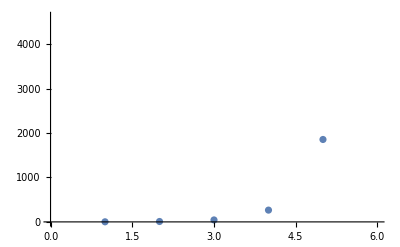

```mathematica
ListPlot[%]
```

```mathematica
Select[Permutations[{1,2,3,4}],cyclepermQ[#,4]&]
```

{{2,1,4,3},{2,3,4,1},{2,4,1,3},{3,1,4,2},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,3,1,2},{4,3,2,1}}